```mathematica
Clear["Global`*"]
```

```mathematica
HA=ℏ({{ωr, 0, 0}, {0, ωe, 0}, {0, 0, ωg}});
HAF=ℏ/2({{0, Ω2 E^(-I ω2 t), 0}, {Conjugate[Ω2] E^(I ω2 t), 0, Ω1 E^(-I ω1 t)}, {0, Conjugate[Ω1] E^(I ω1 t), 0}});
U=({{E^(-ⅈ(ω1+ω2)t), 0, 0}, {0, E^(-I ω1 t), 0}, {0, 0, 1}});
```

```mathematica
ℏ MatrixForm[FullSimplify[1/ℏ(ConjugateTranspose[U].(HA+HAF).U-I ℏ ConjugateTranspose[U].D[U,t]),{t>0,ω1∈Reals,ω2∈Reals}]]
```

ℏ (-ω1-ω2+ωr | Ω2/2 | 0
Conjugate[Ω2]/2 | -ω1+ωe | Ω1/2
0 | Conjugate[Ω1]/2 | ωg)

```mathematica
Htilde=ℏ ({{-Δr, Ω2/2, 0}, {Conjugate[Ω2]/2, -Δe, Ω1/2}, {0, Conjugate[Ω1]/2, ωg}});
ρ=({{σrr[t], σre[t], σrg[t]}, {Conjugate[σre[t]], σee[t], σeg[t]}, {Conjugate[σrg[t]], Conjugate[σeg[t]], σgg[t]}});
```

```mathematica
MatrixForm[D[ρ,t]]
```

(σrr'[t] | σre'[t] | σrg'[t]
Conjugate'[σre[t]] σre'[t] | σee'[t] | σeg'[t]
Conjugate'[σrg[t]] σrg'[t] | Conjugate'[σeg[t]] σeg'[t] | σgg'[t])

```mathematica
MatrixForm[({{σrr'[t], σre'[t], σrg'[t]}, {Conjugate[σre'[t]], σee'[t], σeg'[t]}, {Conjugate[σrg'[t]], Conjugate[σeg'[t]], σgg'[t]}})]==MatrixForm[FullSimplify[1/(I ℏ)(Htilde.ρ-ρ.Htilde),{Ω1>0,Ω2>0,ωg==0}]]
```

```mathematica
({{σrr'[t], σre'[t], σrg'[t]}, {Conjugate[σre'[t]], σee'[t], σeg'[t]}, {Conjugate[σrg'[t]], Conjugate[σeg'[t]], σgg'[t]}})==({{-ⅈ Ω2 (Re[σre[t]]-σre[t]), -1/2 ⅈ (Ω2 σee[t]+2 (Δe-Δr) σre[t]-Ω1 σrg[t]-Ω2 σrr[t]), 1/2 ⅈ (-Ω2 σeg[t]+Ω1 σre[t]+2 Δr σrg[t])}, {1/2 ⅈ (2 (Δe-Δr) Conjugate[σre[t]]-Ω1 Conjugate[σrg[t]]+Ω2 (σee[t]-σrr[t])), -ⅈ (Ω1 Re[σeg[t]]-Ω2 Re[σre[t]]-Ω1 σeg[t]+Ω2 σre[t]), 1/2 ⅈ (Ω1 σee[t]+2 Δe σeg[t]-Ω1 σgg[t]-Ω2 σrg[t])}, {-1/2 ⅈ (-Ω2 Conjugate[σeg[t]]+Ω1 Conjugate[σre[t]]+2 Δr Conjugate[σrg[t]]), -1/2 ⅈ (2 Δe Conjugate[σeg[t]]-Ω2 Conjugate[σrg[t]]+Ω1 (σee[t]-σgg[t])), ⅈ Ω1 (Re[σeg[t]]-σeg[t])}})
```

{{σrr'[t],σre'[t],σrg'[t]},{Conjugate[σre'[t]],σee'[t],σeg'[t]},{Conjugate[σrg'[t]],Conjugate[σeg'[t]],σgg'[t]}}=={{-ⅈ (Re[σre[t]]-σre[t]),-1/2 ⅈ (σee[t]+2 (10-Δr) σre[t]-σrg[t]-σrr[t]),1/2 ⅈ (-σeg[t]+σre[t]+2 Δr σrg[t])},{1/2 ⅈ (2 (10-Δr) Conjugate[σre[t]]-Conjugate[σrg[t]]+σee[t]-σrr[t]),-ⅈ (Re[σeg[t]]-Re[σre[t]]-σeg[t]+σre[t]),1/2 ⅈ (σee[t]+20 σeg[t]-σgg[t]-σrg[t])},{-1/2 ⅈ (-Conjugate[σeg[t]]+Conjugate[σre[t]]+2 Δr Conjugate[σrg[t]]),-1/2 ⅈ (20 Conjugate[σeg[t]]-Conjugate[σrg[t]]+σee[t]-σgg[t]),ⅈ (Re[σeg[t]]-σeg[t])}}

```mathematica
(**)
Ω1=2;
Ω2=2;
Δe=10;
sol=ParametricNDSolve[{σrr'[t]==-Ω2 Im[σre[t]],σee'[t]==-Ω1 Im[σeg[t]]+Ω2 Im[σre[t]],σgg'[t]==Ω1 Im[σeg[t]],σre'[t]==-1/2 ⅈ (Ω2 σee[t]+2 (Δe-Δr) σre[t]-Ω1 σrg[t]-Ω2 σrr[t]),σrg'[t]==1/2 ⅈ (-Ω2 σeg[t]+Ω1 σre[t]+2 Δr σrg[t]),σeg'[t]==1/2 ⅈ (Ω1 σee[t]+2 Δe σeg[t]-Ω1 σgg[t]-Ω2 σrg[t]),σgg[0]==1,σee[0]==0,σrr[0]==0,σre[0]==0,σrg[0]==0,σeg[0]==0},{σgg[t],σee[t],σrr[t],σre[t],σrg[t],σeg[t]},{t,0,10},{Δr}]
```

{σgg[t]→ParametricFunction[<>],σee[t]→ParametricFunction[<>],σrr[t]→ParametricFunction[<>],σre[t]→ParametricFunction[<>],σrg[t]→ParametricFunction[<>],σeg[t]→ParametricFunction[<>]}

```mathematica
Plot3D[Evaluate[{Conjugate[σrr[t][Δr]]σrr[t][Δr]}/.sol],{t,0,10},{Δr,-2,2},AxesLabel->{"t","Δr","σrr"}]
```

-Graphics3D-

```mathematica
(*Testing*)
(**)
Ω1=2;
Ω2=2;
Δe=10;
Γr=.5;
Γe=.075;
sol=ParametricNDSolve[{σrr'[t]==-Ω2 Im[σre[t]]-Γr σrr[t],σee'[t]==-Ω1 Im[σeg[t]]+Ω2 Im[σre[t]]+Γr σrr[t]-Γe σee[t],σgg'[t]==Ω1 Im[σeg[t]]+Γe σee[t],σre'[t]==-1/2 ⅈ (Ω2 σee[t]+2 (Δe-Δr) σre[t]-Ω1 σrg[t]-Ω2 σrr[t]),σrg'[t]==1/2 ⅈ (-Ω2 σeg[t]+Ω1 σre[t]+2 Δr σrg[t]),σeg'[t]==1/2 ⅈ (Ω1 σee[t]+2 Δe σeg[t]-Ω1 σgg[t]-Ω2 σrg[t]),σgg[0]==1,σee[0]==0,σrr[0]==0,σre[0]==0,σrg[0]==0,σeg[0]==0},{σgg[t],σee[t],σrr[t],σre[t],σrg[t],σeg[t]},{t,0,10},{Δr}]
Plot3D[Evaluate[{Conjugate[σrr[t][Δr]]σrr[t][Δr]}/.sol],{t,0,10},{Δr,-2,2},AxesLabel->{"t","Δr","σrr"}]
```

{σgg[t]→ParametricFunction[<>],σee[t]→ParametricFunction[<>],σrr[t]→ParametricFunction[<>],σre[t]→ParametricFunction[<>],σrg[t]→ParametricFunction[<>],σeg[t]→ParametricFunction[<>]}

-Graphics3D-

```mathematica
(**)
```

```mathematica
Solve[{ ({{0, 0, 0}, {0, 0, 0}, {0, 0, 0}})==1/(I ℏ)(ℏ ({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}}).({{σgg, σge, σgr}, {Conjugate[σge], σee, σer}, {Conjugate[σgr], Conjugate[σer], σrr}})-({{σgg, σge, σgr}, {Conjugate[σge], σee, σer}, {Conjugate[σgr], Conjugate[σer], σrr}}).({{0, Ω1/2, 0}, {Ω1/2, -Δe, Ω2/2}, {0, Ω2/2, -Δr}})ℏ)},{σgg,σrr,σee,σge,σgr,σer}]
```

$Aborted

```mathematica
Clear[Δr]
```

{cg[t]→ParametricFunction[<>],ce[t]→ParametricFunction[<>],cr[t]→ParametricFunction[<>]}

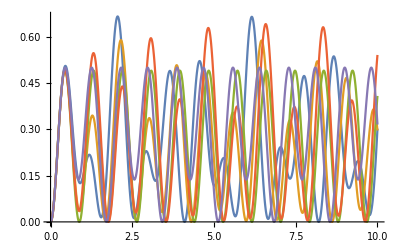

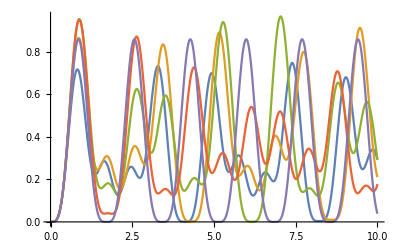

```mathematica
Ω1=5;
Ω2=5;
Δe=1;
ℏ=1;
sol=ParametricNDSolve[{({{cr'[t]}, {ce'[t]}, {cg'[t]}})==ℏ/(I ℏ)({{-Δr, Ω2/2, 0}, {Ω2/2, -Δe, Ω1/2}, {0, Ω1/2, 0}}).({{cr[t]}, {ce[t]}, {cg[t]}}),cg[0]==1,ce[0]==0,cr[0]==0},{cg[t],ce[t],cr[t]},{t,0,10},{Δr}]
Plot[Evaluate[Table[Conjugate[ce[t][Δr]]ce[t][Δr]/.sol,{Δr,-2,2,1}]],{t,0,10},PlotRange->Full]
Plot[Evaluate[Table[Conjugate[cr[t][Δr]]cr[t][Δr]/.sol,{Δr,-2,2,1}]],{t,0,10},PlotRange->Full]
```

```mathematica
Evaluate[Abs[cg[t][3]]^2/.sol]
```

Abs[InterpolatingFunction[{{0., 10.}}, <>][t]]^2